```mathematica
Quit[];
```

```mathematica
mmu=MaxMemoryUsed[]
SetDirectory[NotebookDirectory[]];
(* Global Properties *)
eV=27.211;
h=4.135667516×10^-15;
c=3×10^8;
shell={"s","p","p+","d","d+","f","f+","g","g+"};
RelOrbitals={"4s","5s","4p","4p+","5p","5p+","4d","4d+","5d","5d+","4f","4f+","5f","5f+","5g","5g+"};
jOrbitals={0.5,0.5,0.5,1.5,0.5,1.5,1.5,2.5,1.5,2.5,2.5,3.5,2.5,3.5,3.5,4.5};
(* s must ne first; nj, nj+ must be consecutive *) 
NonRelOrbitals={"4s","5s","4p","5p","4d","5d","4f","5f","5g"};
l={0,0,1,1,2,2,3,3,4};
MaxElectrons=2(2l+1);
spin={0.5,-0.5};

<<ReadAMBiTOutput`;
<<MBQCSpectra`;

FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=600; (* Export Image Resolution dpi *)
```

90595896

```mathematica
NoCIEnergies[fileMBQC_,G_]:=Module[{Shells,EnergyCSF,Num,L,TotalLines,NumTotal,Cutoff,increment,max,min,z,Density,Emin,PsiE},
{
{Shells,EnergyCSF,Num}=ReadLevels[fileMBQC];
L=Length[Shells];
TotalLines=L*(L-1)/2;
EnergyCSF=EnergyCSF eV;
Print["# of CSF averaged states: ",L];
NumTotal=Total[Num];


Cutoff=G; (*Lorenzian has range 2*Cutoff *)
increment=0.005;
max=Max[EnergyCSF]+Cutoff+10;
min=Floor[Min[EnergyCSF]-Cutoff-10];
{z,Density}=LevelDensity[EnergyCSF,Num,G,increment,max,min,Cutoff];

{Emin,PsiE}=ComplexWaveEnergies[G,z,Density,increment,EnergyCSF,Num];
PsiE=PsiE-Emin;
z=z-Emin;
EnergyCSF=EnergyCSF-Emin;
(*EnergyCSF=EnergyCSF-Min[EnergyCSF];*)
};
Return[{L,TotalLines,EnergyCSF,Shells,Num,z,Density}]
]
EigVal[V2_,j_,EnergyCSF_]:=Module[{Eig,M,i},
{
SeedRandom[j];
M=RandomVariate[NormalDistribution[0,V2],{L,L}];
M=(M+Mᵀ)/2;
For[i=1,i≤L,i++,
{
M[[i,i]]=EnergyCSF[[i]];
}];
Eig=Eigenvalues[M];
};
Return[Eig] ;
]

CIEnergies[V2_,EnergyCSF_,G_,MonteCarlo_,Num_,L_]:=Module[{increment,Cutoff,Eig,mean,EnergyCI,max,min,zCI,DensityCI,EminCI,PsiECI,Dspacing},
{
increment=0.005;
Cutoff=G;
Eig=Table[EigVal[V2,i,EnergyCSF],{i,1,MonteCarlo}];
mean=Mean[Eig];
EnergyCI=mean[[Ordering[mean]]];
max=Max[EnergyCI]+Cutoff+10;
min=Floor[Min[EnergyCI]-Cutoff-10];
{zCI,DensityCI}=LevelDensity[EnergyCI,Num,G,increment,max,min,Cutoff];
{EminCI,PsiECI}=ComplexWaveEnergies[G,zCI,DensityCI,increment,EnergyCI,Num];
PsiECI=PsiECI-EminCI;
zCI=zCI-EminCI;
EnergyCI=EnergyCI-EminCI;
(*PsiECI=PsiECI-Min[EnergyCI];
zCI=zCI-Min[EnergyCI];
EnergyCI=EnergyCI-Min[EnergyCI];
EminCI=Min[PsiECI];*)
Dspacing=Table[LevelSpacing[PsiECI,EnergyCI[[i]],G],{i,1,L}];
};
Return[{EnergyCI,Dspacing,zCI,DensityCI,EminCI}]
]

PartitionValue[EnergyCI_,Temp_,Num_,L_,EminCI_]:=Module[{Z},
{
Z=Total[Table[Num[[i]]*Exp[-(EnergyCI[[i]](*-EminCI*))/Temp],{i,1,L}]];
};
Return[Z]
]

StatisticalValues[G_,EnergyCI_,EnergyCSF_,Num_,Shells_,L_]:=Module[{Components,Components2,CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs,AverageJ,AverageJall,i,pos,Jinitial,nAverage},
{
Components=ComplexCoefficients2[G,EnergyCI,EnergyCSF,Num,2*G];
Components2=Components^2;
{CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs}=NonRelativisticConfiguration[Shells,Num];
AverageJ=ConigurationAverageJ[CONFIGS];
AverageJall=ConstantArray[0,Length[NonRelConfigs]];
For[i=1,i≤Length[CONFIGS],i=i+1,
{
pos=Position[NonRelConfigs,CONFIGS[[i]]];
AverageJall[[posᵀ[[1]]]]=AverageJ[[i]];
}];
Jinitial=Table[Total[AverageJall*Components[[i]]]/Total[Components[[i]]],{i,1,L}];
nAverage=(RelConfigsᵀ/(2*jOrbitals+1))ᵀ;

};
Return[{Components2,Jinitial,nAverage}]
]
EnergyImages[EnergyCI_,EnergyCSF_,L_]:=Module[{imEn,i,s1,EnergyCI2,EnergyCSF2},
{
EnergyCI2=EnergyCI(*-Min[EnergyCI]*);
EnergyCSF2=EnergyCSF(*-Min[EnergyCSF]*);
imEn={};
For[i=1,i≤L,i++,
{
AppendTo[imEn,ListPlot[{{EnergyCSF2[[i]],0.05},{EnergyCSF2[[i]],0.45}},PlotStyle->Black,Joined->True]];
AppendTo[imEn,ListPlot[{{EnergyCI2[[i]],0.55},{EnergyCI2[[i]],0.95}},PlotStyle->Blue,Joined->True]]
}];
s1=Show[imEn,AspectRatio->1/3,ImageSize->Large,PlotRange->All]
};
Return[s1]
]

LineStrengthsCI[T_,EnergyCI_,EnergyCSF_,indicies_,Num_,Jinitial_,Dspacing_,Components2_,TotalLines_,E1_,G_,L_]:=Module[{mel,ω,Lmel,UppEnergyList,LowEnergyList,Photon,UppIndList,LowIndList,UppNList,LowNList,NList,JuppList,DlowList,W1,W2,S,Nactual,Ntotal,i,j,P,m,wab,P2,exp,UppStateInd,LowStateInd,UppNoCIEnergy,LowNoCIEnergy,Lorentzian,LorentzianNorm,w1,w2,Theta,num,SList,Strength,NT,NA,Sall,pos,WeightsAll,WeightsOk},
{
mel=Tᵀ[[1]];
ω=Tᵀ[[2]];
Lmel=Length[mel];

UppEnergyList=EnergyCI[[indicies[[2]]]];
LowEnergyList=EnergyCI[[indicies[[1]]]];
Photon=UppEnergyList-LowEnergyList;
UppIndList=indicies[[2]];
LowIndList=indicies[[1]];
UppNList=Num[[UppIndList]];
LowNList=Num[[LowIndList]];
NList=UppNList*LowNList;
JuppList=Jinitial[[UppIndList]];
DlowList=Dspacing[[LowIndList]];
W1=Components2[[UppIndList]];
W2=Components2[[LowIndList]];

S=ConstantArray[0,{TotalLines,Lmel}];

For[i=1,i≤TotalLines,i++,
{
For[j=1,j≤Lmel,j++,
{
P=Position[E1,j];
If[P≠{},
{
m=mel[[j]];
wab=ω[[j]];
P2=P;
P2[[All,3]]=2;
exp=Extract[E1,P2];
UppStateInd=P[[All,1]];
LowStateInd=P[[All,2]];
UppNoCIEnergy=EnergyCSF[[Pᵀ[[1]]]];
LowNoCIEnergy=EnergyCSF[[Pᵀ[[2]]]];
(*UppNoCIEnergy=EnergyCI[[Pᵀ[[1]]]];
LowNoCIEnergy=EnergyCI[[Pᵀ[[2]]]];*)
(*Δ=wab-(UppEnergyList[[i]]-LowEnergyList[[i]]);*)
Δ=(UppNoCIEnergy-LowNoCIEnergy)-(UppEnergyList[[i]]-LowEnergyList[[i]]);
(*Δ=wab+(UppEnergyList[[i]]-UppNoCIEnergy)-(LowEnergyList[[i]]-LowNoCIEnergy)-(UppEnergyList[[i]]-LowEnergyList[[i]]);*)
Lorentzian=1/(2π) *(2G)/(Δ^2+(2G)^2/4);

w1=W1[[i,UppStateInd]];
w2=W2[[i,LowStateInd]];
Theta=Sign[w1*w2];

(*S[[i,j]]=Total[m*LorentzianNorm*w1*exp*Theta]*);
S[[i,j]]=Total[m*Lorentzian*w1*exp*Theta];
}];
}];
}];
SList=Total[S,{2}];
Strength=NList*(2*JuppList+1)*DlowList*SList/3;

Print["Done calculating S"];
};
Return[{Photon,Strength,UppEnergyList,LowEnergyList,NList}];
]

LineIntensityCI[Photon_,Strength_,UppEnergyList_,Temp_,Z_,EminCI_]:=Module[{Einstein,Intensity},
{
Einstein=(2.0261*10^18)*(Photon)^3/(4.1357*10^-15*3*10^8*10^10)^3 *Strength;
Intensity=Exp[-(UppEnergyList-EminCI)/Temp]*Einstein*Photon/(4π Z);
};
Return[{Einstein,Intensity}]
]

SpectrumImages[AR_,axis_,discrete_,MBQCx_,MBQCy_,CIx_,CIy_,Diagx_,Diagy_,EnergyRange_,MBQCSpectrum_,CISpectrum_,Diag0Spectrum_,ylabel_]:=Module[{s1,im1,im2,imA,imB,imX,imY},
{

If[discrete==True,
{
im1=ListPlot[{MBQCx,MBQCy}ᵀ,PlotRange->axis,Filling->Axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic];
imA=ListPlot[{CIx,CIy}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
imX=ListPlot[{Diagx,Diagy}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
im2=ListLinePlot[{EnergyRange,MBQCSpectrum}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CISpectrum}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Spectrum}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s1=Show[{imA,imB,imX,imY,im1,im2},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ω (eV)",ylabel},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],ImageSize->Large]
},{
im2=ListLinePlot[{EnergyRange,MBQCSpectrum}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CISpectrum}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Spectrum}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s1=Show[{imB,imY,im2},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ω (eV)",ylabel},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],ImageSize->Large]
}];
};
Return[s1]
]
```

# Code Starts Here

```mathematica
ION="12";
configs="df-df-0";
filenameMBQC="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileMBQC=Import[filenameMBQC,"CSV"];
filenameCI="E1_Transitions3/Sn"<>ION<>"/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileCI=Import[filenameCI,"CSV"];
(*filename0diag="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";*)
file0diag=(*Import[filename0diag,"CSV"];*)fileMBQC;
```

# of CSF averaged states: 42

Total number of MBQC Lines = 861

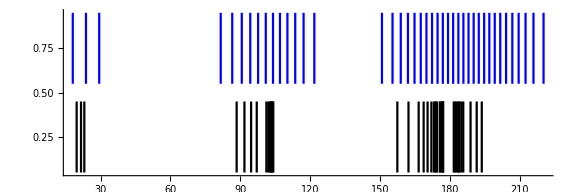

```mathematica
(* Sn08 -> 15, Sn09 -> 16, Sn10 -> 17, Sn11 -> 20, Sn12 -> 22, Sn13 -> 23, Sn14 -> 24*)
G=22;
Temp=26;
{L,TotalLines,EnergyCSF,Shells,Num,z,Density}=NoCIEnergies[fileMBQC,G];
Print["Total number of MBQC Lines = ",TotalLines]
T=SingleTransitionData[fileMBQC];
Ltran=Length[T];
If[configs=="d-0",V=2.5];
If[configs=="f-0",V=1.6];
If[configs=="df-0",V=2];
If[configs=="df-df-0",V=2.2];
If[configs=="df-df-df-0",V=1.5];
If[configs=="Range2",V=0.61];
V2=V^2;
MonteCarlo=1000;
{EnergyCI,Dspacing,zCI,DensityCI,EminCI}=CIEnergies[V2,EnergyCSF,G,MonteCarlo,Num,L];
EnergyImages[EnergyCI,EnergyCSF,L]
Z=PartitionValue[EnergyCI,Temp,Num,L,EminCI];
{Components2,Jinitial,nAverage}=StatisticalValues[G,EnergyCI,EnergyCI(*EnergyCSF*),Num,Shells,L];
E1=Table[E1Transitions[i,j,Shells,T,nAverage],{i,1,L},{j,1,L}];
indicies=ListIndicies[L];
```

```mathematica
fCI=ReadCI[fileCI];
EnergyfCI=Flatten[fCI[[All,All,4,All,2]]];
EnergyfCI=EnergyfCI-Min[EnergyfCI];
EnergyfCI=EnergyfCI*27.211;
fNoCI=ReadCI[file0diag];
EnergyfNoCI=Flatten[fNoCI[[All,All,4,All,2]]];
EnergyfNoCI=EnergyfNoCI-Min[EnergyfNoCI];
EnergyfNoCI=EnergyfNoCI*27.211;
imNoCI={}
imCI={}
For[i=1,i≤Length[EnergyfCI],i++,
{
AppendTo[imNoCI,ListPlot[{{EnergyfNoCI[[i]],0.05},{EnergyfNoCI[[i]],0.45}},PlotStyle->Black,Joined->True]];
AppendTo[imCI,ListPlot[{{EnergyfCI[[i]],1.05},{EnergyfCI[[i]],1.45}},PlotStyle->Blue,Joined->True]]
}];

imAvNoCI={};
imAvCI={};
For[i=1,i≤L,i++,
{
AppendTo[imAvNoCI,ListPlot[{{EnergyCSF[[i]]-Min[EnergyCSF],0.55},{EnergyCSF[[i]]-Min[EnergyCSF],0.95}},PlotStyle->{Black,Dashed},Joined->True,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->1/3]];
AppendTo[imAvCI,ListPlot[{{EnergyCI[[i]]-Min[EnergyCI],1.55},{EnergyCI[[i]]-Min[EnergyCI],1.95}},PlotStyle->{Blue,Dashed},Joined->True,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->1/3]]
}];
```

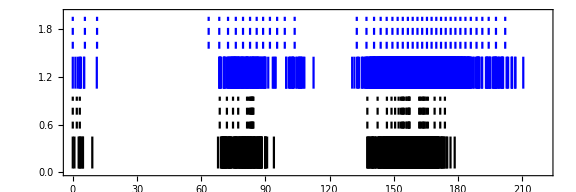

```mathematica
Show[{imNoCI,imCI,imAvNoCI,imAvCI},Frame->{True,False,False,False},PlotRangePadding->0,FrameLabel->{"E (eV)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],PlotRange->{{0,220},{0,2}},AspectRatio->1/3]
```

```mathematica
Tic=AbsoluteTime[];
{Photon,StrengthOrig,UppEnergyList,LowEnergyList,NList}=LineStrengthsCI[T,EnergyCI,EnergyCSF,indicies,Num,Jinitial,Dspacing,Components2,TotalLines,E1,G,L];
Toc=AbsoluteTime[];
Print[Toc-Tic];
```

Done calculating S

17.804935

```mathematica
highcut=100; (*12.4nm*)
lowcut=90; (*13.78nm*)
StrengthTotal=Total[StrengthOrig];
Nband=NList*UnitStep[Photon-lowcut]*UnitStep[highcut-Photon];
(*PhotonCentre=Photon[[Position[StrengthOrig/NList,Max[StrengthOrig/NList]][[1]]]][[1]];*)
PhotonCentre=Photon[[Position[Nband,Max[Nband]][[1]]]][[1]]

a={50,130,225}
weight={2,1}
InitialFactor=ConstantArray[0,Length[UppEnergyList]];

For[i=1,i≤Length[UppEnergyList],i++,
{
If[118<UppEnergyList[[i]]≤ 122,InitialFactor[[i]]=weight[[1]]];
If[207<UppEnergyList[[i]]≤225&& 105<LowEnergyList[[i]]<125,InitialFactor[[i]]=weight[[2]]];
}];
(*Strength=1/(π)(G/8)/((Photon-PhotonCentre)^2+(G/8)^2)*InitialFactor;
(*sigma=(G/4)/Sqrt[2Log[2]];
Strength=1/Sqrt[2π sigma^2]*Exp[-(PhotonCentre-Photon)^2/(2 sigma^2)]*InitialFactor;*)
Strength=Strength/Total[Strength]*StrengthTotal;*)

(*PhotonBandPass=UnitStep[highcut-Photon]*UnitStep[Photon-lowcut];*)
(*StrengthBandPass=StrengthOrig*PhotonBandPass;*)
StrengthBandPass=StrengthOrig*InitialFactor;
Strength=StrengthBandPass/Total[StrengthBandPass]*StrengthTotal;


pos=Position[UppEnergyList,EnergyCI[[40]]]ᵀ[[1]];
ListPlot[{{Photon,StrengthBandPass}ᵀ,{Photon[[pos]],StrengthBandPass[[pos]]}ᵀ},PlotRange->{{70,120},All},Filling->Axis,PlotStyle->{Blue,Black},ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic]

(*Strength=StrengthOrig;*)
```

92.966

{50,130,225}

{2,1}

```mathematica
{Einstein,Intensity}=LineIntensityCI[Photon,Strength,UppEnergyList,Temp,Z,EminCI];
```

```mathematica
{ECI,SCI,EINITIAL,EFINAL,IntensityCI,EinsteinCI}=DiscreteLevels[fileCI,Temp];
Print["Done CI"]
{Ediag,Sdiag,EINITIALdiag,EFINALdiag,Intensitydiag,Einsteindiag}=DiscreteLevels[file0diag,Temp];
Print["Done NoOffDiag"]
```

Done CI

Done NoOffDiag

```mathematica
spread=2;
EnergyRange=Range[0,300,0.1];
```

```mathematica
MBQCSpectrum=DiscreteSpectrum[Photon,Strength,EnergyRange,spread];
Print["1"]
MBQCIntensity=DiscreteSpectrum[Photon,Intensity,EnergyRange,spread];
Print["4"]
```

1

4

```mathematica
CISpectrum=DiscreteSpectrum[ECI,SCI,EnergyRange,spread];
Print["2"]
Diag0Spectrum=DiscreteSpectrum[Ediag,Sdiag,EnergyRange,spread];
Print["3"]
CIIntensity=DiscreteSpectrum[ECI,IntensityCI,EnergyRange,spread];
Print["5"]
Diag0Intensity=DiscreteSpectrum[Ediag,Intensitydiag,EnergyRange,spread];
Print["6"]
```

2

3

5

6

```mathematica
Total[Strength]
Total[SCI]
```

2626.88

2706.99

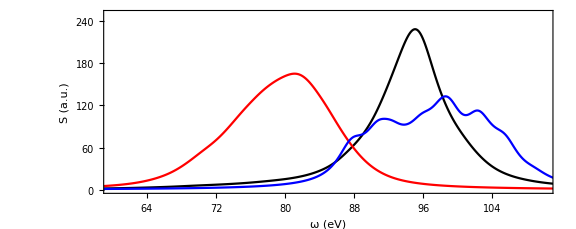

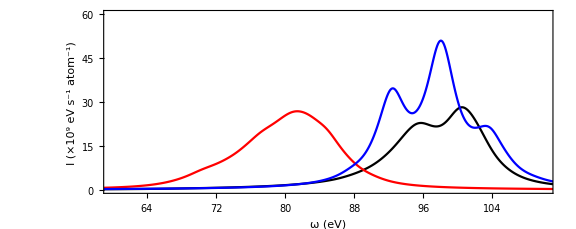

```mathematica
AR=1/2.5;
discrete=False;
axis={{60,110},{0,250}};
SpectrumImages[AR,axis,discrete,Photon,Strength,ECI,SCI,Ediag,Sdiag,EnergyRange,MBQCSpectrum,CISpectrum,Diag0Spectrum,"S (a.u.)"]
axis={{60,110},{0,6*10^1}};
SpectrumImages[AR,axis,discrete,Photon,Intensity/10^9,ECI,IntensityCI/10^9,Ediag,Intensitydiag/10^9,EnergyRange,MBQCIntensity/10^9,CIIntensity/10^9,Diag0Intensity/10^9,"I (×10^9 eV s^-1 atom^-1)"]
```